

4

{}

{}

{}

«9 more identical outputs»

{1}

Checkpoint 1

Checkpoint 1

{1,2}

Checkpoint 1

Checkpoint 2

Checkpoint 3

{1}

End of Checkpoint 3

Checkpoint 1

{1,2,3}

Checkpoint 1

Checkpoint 2

Checkpoint 3

{1}

End of Checkpoint 3

Checkpoint 3

{2}

End of Checkpoint 3

Checkpoint 1

{1,2,3,4}

Checkpoint 1

Checkpoint 2

Checkpoint 3

{1,2,3,4}

{1}

End of Checkpoint 3

Checkpoint 2

Checkpoint 3

{2,3,4}

{2}

End of Checkpoint 3

Checkpoint 2

Checkpoint 3

{3,4}

{3}

End of Checkpoint 3

Checkpoint 1

{{2},{3},{},{}}

{-1,1,2,-1}

{}

{2}

{3}

{}

{}

{{2},{3},{},{}}

{1,2,3,4}

{}

Wow1!

Wow2!

{slope→-0.57735,intcpt→0.57735}

-0.57735

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Hello

-0.57735

0.57735

False

Hello

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

False

Wow2!

{slope→-0.57735,intcpt→1.26217}

-0.57735

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Hello

-0.57735

1.26217

False

Wow2!

{slope→-1.2379,intcpt→2.58988}

-1.2379

Wow1!

Wow2!

{slope→3.73205,intcpt→3.73205}

3.73205

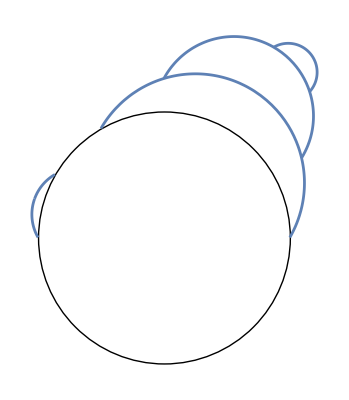

output.png

1

-Graphics-

-Graphics-

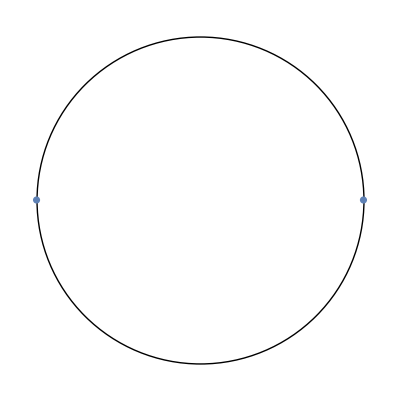

{}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1.09543

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-2.38678+0.12698 ⅈ

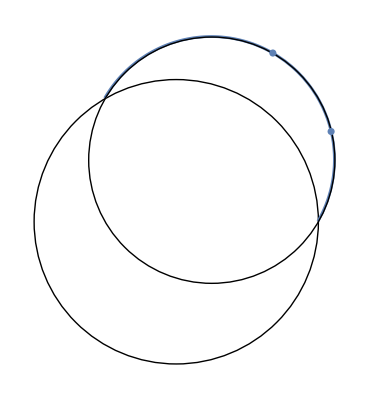

```mathematica
circle = Graphics[Circle[{0, 0}, 1]]
n = Input["Enter the number of pairs"]
pointlst = {}
pointlst1 = {}
parentlst = {}
childlst = {}
startlst = {}
endlst = {}
bendlst = {}
bent = {}
a = {}
b = {}
c = {}
d = {}
For[i=1, i≤n, i++,
pointlst1 = Join[pointlst1, {i}];
Print[pointlst1];
parentlst = Join[parentlst, {-1}];
childlst = Join[childlst, {{}}];
angles = Input["Enter angles of points of pair" ];
bend =Input["Enter the angle of bending for this pair"];
startlst = Join[startlst, {angles[[1]]}];
endlst = Join[endlst, {angles[[2]]}];
bendlst = Join[bendlst, {bend}];
pointlst = Join[pointlst, {{{Cos[angles[[1]]], Sin[angles[[1]]]}, {Cos[angles[[2]]], Sin[angles[[2]]]}, bend}}];
p1 = pointlst[[i]][[1]][[1]]+I*pointlst[[i]][[1]][[2]];
p2 = pointlst[[i]][[2]][[1]]+I*pointlst[[i]][[2]][[2]];
k = Norm[p1+p2];
const = (-((2-k)/k)(p1+p2)+I(p2-p1))/(((2-k)/k)(p1+p2)+I(p2-p1));
c = Join[c, { Sqrt[1/(const((p1+p2)/2-I*const*(p1-p2)/2)-((p1+p2)(2-k)/(2k)-const(p1+p2)/k-I*const(p1-p2)/2))]}];
d =Join[d, {c[[i]]*const}];
a = Join[a, {(c[[i]](p1+p2)-I*d[[i]](p2-p1))/2}];
b = Join[b, {((c[[i]](p1+p2)(2-k)/(2k))+d[[i]]((p1+p2)/k+I*(p2-p1)/2))}];
templst = pointlst1;
Print["Checkpoint 1"];
While[templst ≠{i},
Print["Checkpoint 2"];
temp = {templst[[1]]};
While[temp ≠ {},
Print["Checkpoint 3"];
If[angles[[1]] ≥ startlst[[temp[[1]]]]&&angles[[2]] ≤ endlst[[temp[[1]]]],
parentlst = ReplacePart[parentlst, i->temp[[1]]];
templst = DeleteElements[templst, temp];
Print[temp];
temp = childlst[[temp[[1]]]];
Print["End of Checkpoint 3"];,
Print[templst];
templst = DeleteElements[templst, temp];
Print[temp];
temp = DeleteElements[temp, {temp[[1]]}];
Print["End of Checkpoint 3"];];
]
];
If[parentlst[[i]] ≠ -1,
joined = Join[childlst[[parentlst[[i]]]], {i}];
childlst = ReplacePart[childlst, parentlst[[i]]->joined];
];
templst = pointlst1;
Print["Checkpoint 1"];
flag = -1;
For[j = 1, j<i, j++,
If[angles[[1]] ≤ startlst[[j]]&&angles[[2]] ≥ endlst[[j]],
flag = j;
Break;]
]
If[flag ≠ -1,
While[angles[[1]] ≤ startlst[[flag]]&&angles[[2]] ≥ endlst[[flag]],
flag = parentlst[[flag]];];
temp = childlst[[flag]];
k = Length[temp];
For[g = 1, g≤k, g++,
If[angles[[1]] ≤ startlst[[g]]&&angles[[2]] ≥ endlst[[g]],
joined = Join[childlst[[i]], {temp[[g]]}];
childlst = ReplacePart[childlst, i->joined];]]]]
childlst
parentlst
newchildlst = {}
For[i = 1, i≤n, i++,
tempchild = childlst[[i]];
Print[tempchild];
l = Length[tempchild];'
If[l>0,
tempnewchild  = {tempchild[[1]]};
If[l≥2,
For[j = 2, j≤l, j++,
k = j-1;
tempnewchild = Join[tempnewchild, {tempchild[[j]]}];
While[k>0 && startlst[[tempnewchild[[k]]]]≥ startlst[[tempchild[[j]]]],
tempnewchild = ReplacePart[tempnewchild, (k+1)->tempnewchild[[k]]];
k-=1;
];
rep = tempchild[[j]];
tempnewchild = ReplacePart[tempnewchild, k+1->rep];
];
];
newchildlst = Join[newchildlst, {tempnewchild}],
newchildlst = Join[newchildlst, {{}}]]
];
childlst = newchildlst
templst = pointlst1
newpointlst = {}
While[templst ≠ {},
Print["Wow1!"];
temp = templst[[1]];
While[parentlst[[temp]] ≠ -1,
temp = parentlst[[temp]]
];
queue = {temp};
While[queue ≠ {},
Print["Wow2!"];
temp = queue[[1]];
t = Tan[pg];
theta  = pointlst[[temp]][[3]];
theta =-theta;
m =Limit[Tan[w], w->theta, Direction->"FromAbove"];
If[theta == -Pi/2, x = 0;
y = (t^2-4)/((-2+t)^2), If[theta == Pi/2, x=0; y=(t^2-4)/((2+t)^2),
y =(t^2+(m*t)^2-4)/(t^2+((m*t)+2)^2);
x = 4*t/(t^2+((m*t)+2)^2)]];
point = x+I*y;
fpoint = (a[[temp]]*point+b[[temp]])/(c[[temp]]*point+d[[temp]]);
If[-Pi/2≤-theta≤Pi/2,bent = Join[bent, {ParametricPlot[{Re[fpoint], Im[fpoint]}, {pg, 0, Pi/2}, PlotStyle->Automatic]}]
,
bent = Join[bent,{ParametricPlot[{Re[fpoint],Im[fpoint]}, {pg, Pi/2, Pi}, PlotStyle->Automatic]}]];
queue = DeleteElements[queue, {temp}];
templst = DeleteElements[templst, {temp}];
tempchild = childlst[[temp]];
pts = Table[{Re[fpoint], Im[fpoint]} /. pg -> val, {val, 0, Pi/2, 0.1}];
ptsd = Table[{Re[fpoint], Im[fpoint]} /. pg -> val, {val, Pi/2, 0,-0.1}];
{x1, y1} = pts[[1]];
{x2, y2} = pts[[2]];
{x3, y3} = pts[[3]];
pt1d = pts[[1]];
pts1d = ptsd[[1]];
Clear[slope, intcpt];
eqns = {
slope*pt1d[[1]]+intcpt == pt1d[[2]],
slope*pts1d[[1]]+intcpt == pts1d[[2]]
};
solution =Solve[eqns, {slope, intcpt}][[1]];
Print[solution];
{Global`slope, Global`intcpt} = {slope, intcpt}/.solution;
Print[slope];
Clear[h, g, r];
eqns = {
   (x1 - h)^2 + (y1 - g)^2 == r^2,
   (x2 - h)^2 + (y2 - g)^2 == r^2,
   (x3 - h)^2 + (y3 - g)^2 == r^2
};
solution = Solve[eqns, {h, g, r}];
solution = solution[[2]];
h = h/.solution[[1]];
g = g/.solution[[2]];
r = r/.solution[[3]];
circless = Graphics[{Circle[{h, g}, r]}];
l = Length[tempchild];
If[l>0,
For[i = 1, i≤l, i++,
Print["Hello"];
Print[slope];
Print[intcpt];
lem = tempchild[[i]];
queue = Join[queue, {tempchild[[i]]}];
pt = pts[[3]];
npt = Norm[pt];
set = {-3Pi/2, -Pi/2, Pi/2, 3Pi/2};
If[MemberQ[set, endlst[[lem]]] ||MemberQ[set,startlst[[lem]] ] ,
If[MemberQ[set,startlst[[lem]]] ,
pt1 ={0,g+Sqrt[r^2-h^2]};
If[(slope*pt1[[1]]+intcpt-pt1[[2]])(slope*pt[[1]]+intcpt-pt[[2]])<0,pt1 = {0, g-Sqrt[r^2-h^2]}; , ];
m2 = Tan[endlst[[tempchild[[i]]]]];
is21 = ((h+m2*g)+Sqrt[2m2*g*h-g^2+r^2-(m2*h)^2+(m2*r)^2])/(1+m2^2);
is22 = ((h+m2*g)-Sqrt[2m2*g*h-g^2+r^2-(m2*h)^2+(m2*r)^2])/(1+m2^2);
pt2 ={is22, m2*is22};
If[(slope*pt2[[1]]+intcpt-pt2[[2]])(slope*pt[[1]]+intcpt-pt[[2]])<0, pt2 = {is21, m2*is21},],
pt2 ={0,g+Sqrt[r^2-h^2]};
Print[(slope*pt2[[1]]+intcpt-pt2[[2]])(slope*pt[[1]]+intcpt-pt[[2]])<0];
If[(slope*pt2[[1]]+intcpt-pt2[[2]])(slope*pt[[1]]+intcpt-pt[[2]])<0,pt2 = {0, g-Sqrt[r^2-h^2]}; Print["Hello"],Print["Hello"] ];
m1 = Tan[startlst[[tempchild[[i]]]]];
is11 = ((h+m1*g)+Sqrt[2m1*g*h-g^2+r^2-(m1*h)^2+(m1*r)^2])/(1+m1^2);
is12 = ((h+m1*g)-Sqrt[2m1*g*h-g^2+r^2-(m1*h)^2+(m1*r)^2])/(1+m1^2);
 pt1 ={is12, m1*is12};
If[(slope*pt1[[1]]+intcpt-pt1[[2]])(slope*pt[[1]]+intcpt-pt[[2]])<0,pt1 = {is11, m1*is11};, 
]];
,
m1 = Tan[startlst[[tempchild[[i]]]]];
m2 = Tan[endlst[[tempchild[[i]]]]];
is11 = ((h+m1*g)+Sqrt[2m1*g*h-g^2+r^2-(m1*h)^2+(m1*r)^2])/(1+m1^2);
is12 = ((h+m1*g)-Sqrt[2m1*g*h-g^2+r^2-(m1*h)^2+(m1*r)^2])/(1+m1^2);
is21 = ((h+m2*g)+Sqrt[2m2*g*h-g^2+r^2-(m2*h)^2+(m2*r)^2])/(1+m2^2);
is22 = ((h+m2*g)-Sqrt[2m2*g*h-g^2+r^2-(m2*h)^2+(m2*r)^2])/(1+m2^2);
 pt1 ={is12, m1*is12};
pt2 ={is22, m2*is22};
If[(slope*pt1[[1]]+intcpt-pt1[[2]])(slope*pt[[1]]+intcpt-pt[[2]])<0,pt1 = {is11, m1*is11};, 
];
If[(slope*pt2[[1]]+intcpt-pt2[[2]])(slope*pt[[1]]+intcpt-pt[[2]])<0, pt2 = {is21, m2*is21},];];
ptplot = ListPlot[{pt1, pt2}];
Clear[a1, b1, c1, d1];
p1 = pointlst[[lem]][[1]][[1]]+I*pointlst[[lem]][[1]][[2]];
p2 = pointlst[[lem]][[2]][[1]]+I*pointlst[[lem]][[2]][[2]];
k = Norm[p1+p2];
eqns = {
(a1*p1+b1) == (pt1[[1]]+I*pt1[[2]])(c1*p1+d1),
(a1*p2+b1) == (pt2[[1]]+I*pt2[[2]])(c1*p2+d1),
a1*d1-b1*c1 == 1,
(a1*(p1+p2)/k+b1) == ((pt1[[1]]+pt2[[1]]-2h+I*(pt1[[2]]+pt2[[2]]-2g))*r/Norm[ (pt1[[1]]+pt2[[1]]-2h+I*(pt1[[2]]+pt2[[2]]-2g))]+(h+I*g))(c1*(p1+p2)/k+d1)
};
solution = Solve[eqns, {a1, b1, c1, d1}][[1]];
{a1, b1, c1, d1} = {a1, b1, c1, d1}/. solution;
Print[a1==a[[temp]]];
ptplt = ListPlot[{{Re[(a1*p1+b1)/(c1*p1+d1)],Im[(a1*p1+b1)/(c1*p1+d1)] }, {Re[p1], Im[p1]}, {Re[p2], Im[p2]}}];
{atemp, btemp, ctemp, dtemp} = {a[[lem]], b[[lem]], c[[lem]], d[[lem]]};
a = ReplacePart[a, lem->(atemp*a1+ctemp*b1)];
b =ReplacePart[b, lem->(btemp*a1+dtemp*b1)];
c = ReplacePart[c, lem->(atemp*c1+ctemp*d1)];
d = ReplacePart[d, lem->(btemp*c1+dtemp*d1)];
];
Clear[slope, intcpt];
];
];
Clear[h, g, r];
]

Output = Show[circle, bent,  PlotRange->Full]
Export["output.png", Output]
```

```mathematica
ClearAll["Global`*"]
```

ReplaceAll::reps: {ParametricRegion[{{Cos[v] u,u Sin[v]},0≤u≤1&&0≤v≤2 π},{u,v}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Reduce::naqs: {(4 Tan[pg])/(Tan[«1»]^2+Plus[«2»]^2)==0.5,(-4+4/3 Tan[«1»]^2)/(Tan[«1»]^2+Plus[«2»]^2)==0.5}/.ParametricRegion[{{Cos[v] u,u Sin[v]},0≤u≤1&&0≤v≤2 π},{u,v}] is not a quantified system of equations and inequalities.

Reduce[{(4 Tan[pg])/(Tan[pg]^2+(2-Tan[pg]/(√3))^2)==0.5,(-4+(4 Tan[pg]^2)/3)/(Tan[pg]^2+(2-Tan[pg]/(√3))^2)==0.5}/.ParametricRegion[{{Cos[v] u,u Sin[v]},0≤u≤1&&0≤v≤2 π},{u,v}],{u,v}]